FittedModel[0.368421+0.000115264 x]

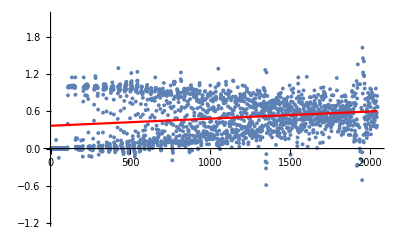

0.53822

{1.95605×10^-69,1.63331×10^-11}

```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
name := "forall-fixed-i"
data :=Import[StringJoin["/Users/greg/Documents/School/Science_Research/workspace/ODRA-with-Enums/greg/queries/benchmarks-",name,".csv"], "Table", {"FieldSeparators" -> ";"}][[All,{1,3}]]
nlm = NonlinearModelFit[data, a+b*x,{a,b},x]
Show[ListPlot[data],Plot[nlm[x],{x,0,2048},PlotStyle->Red]]
nlm["RSquared"]
nlm["ParameterPValues"]
```